```mathematica
(* Jack Morris - 04/30/17 *)
aNote[x_]:=Sin[1100π*x]
Play[aNote[t],{t,0,5}]
```

-Graphics-

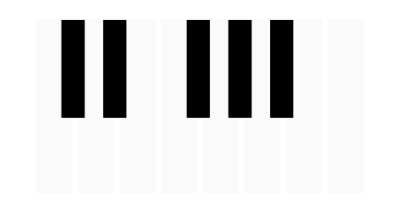

```mathematica
(* Eight ivory rectangles next to each other *)
Ivory=RGBColor[0.98,0.98,0.98];
whiteKeyWidth = 20;
whiteKeyHeight=100;
whiteKeyPadding=4;
whiteKeyTopLeftCorners=NestList[{#[[1]]+whiteKeyWidth+whiteKeyPadding,#[[2]]}&,{0,0},7];
whiteKeyBotRightCorners={whiteKeyWidth,whiteKeyHeight}+#&/@whiteKeyTopLeftCorners;
whiteRectangles=MapThread[Rectangle,{whiteKeyTopLeftCorners,whiteKeyBotRightCorners}];
whiteKeyDisplay=Join[{EdgeForm[Thick],Ivory},whiteRectangles];

(* Eight black keys *)
blackCorners={{#[[1]][[1]]+(whiteKeyWidth)/2+whiteKeyPadding,#[[2]][[2]]*3/7},{#[[2]][[1]]+(whiteKeyWidth-whiteKeyPadding)/2,#[[2]][[2]]}}&/@whiteRectangles;
blackRectangles=Rectangle[#[[1]],#[[2]]]&/@blackCorners;
blackKeyDisplay=Join[{Black},blackRectangles];

(* Remove three black keys *)
blackRectangles=blackRectangles[[;;6]];
blackRectangles=Delete[blackRectangles,3];
blackKeyDisplay=Join[{Black},blackRectangles];

(* Display all *)
allKeys=Join[whiteKeyDisplay,blackKeyDisplay];
Graphics[allKeys]
```

```mathematica
Clear[*]
```